```mathematica
ClearAll/@{checkMonotonic,interpolate};
checkMonotonic[points_]:=Module[{yp,c1,c2},
yp=Transpose[points][[2]];
c1=And@@Table[yp[[i]]<yp[[i+1]],{i,Length@yp-1}];
c2=And@@Table[yp[[i]]>yp[[i+1]],{i,Length@yp-1}];
c1||c2
]
interpolate[points_,y_]:=Module[
{n,tp,xp,yp,res},
tp=Transpose@points;
xp=tp[[1]];
yp=tp[[2]];
n=Length@xp;
res=Sum[Product[If[j!=k,(y-yp[[j]])/(yp[[k]]-yp[[j]]),1],{j,1,n}]xp[[k]],{k,1,n}];
res
]
test[p_,n_]:=Module[
{res,min,max,tp},
tp=Transpose@p;
If[!checkMonotonic[p],Return[]];
max=Max[tp[[2]]];
min=Min[tp[[2]]];
res=Table[{interpolate[p,i],i},{i,min,max,(max-min)/n}];
Show[
ListPlot[p,PlotStyle->Blue],
ListLinePlot[res,PlotStyle->Red]
]
]
```

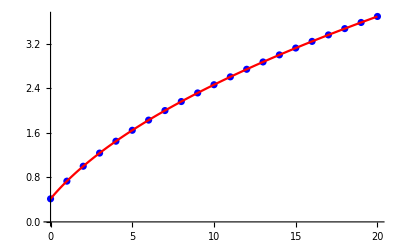

```mathematica
p1=Table[{i,N@Sqrt[i+2]-1},{i,0,20}];
test[p1,100]
```

```mathematica
p2=Table[{i,(i-1)^2},{i,-2,20}];
test[p2,100]
```

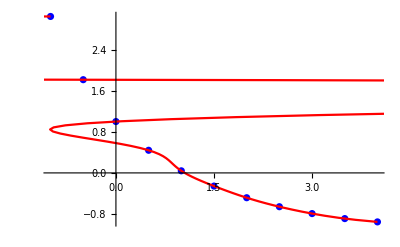

```mathematica
p3=Table[{i,E^-i+Sin[-i/3]},{i,-1,4,0.5}];
test[p3,100]
```